# Integral 1 for N3AS

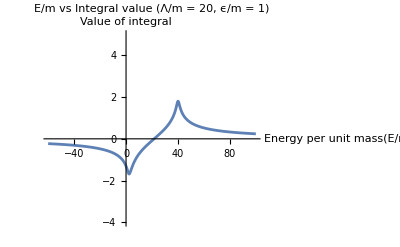

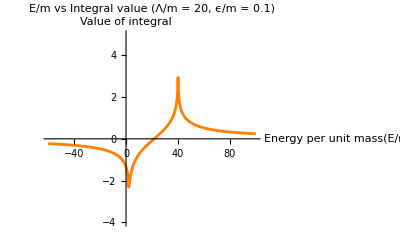

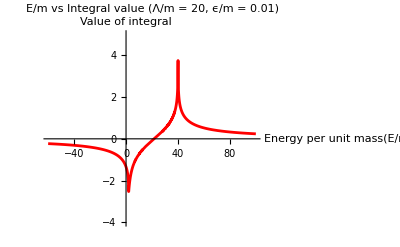

```mathematica
f[x_, A_, ϵ_] := x^2/((x^2+1)(A-2√(x^2+1)+ⅈ ϵ)); 
Int[A_,Λ_, ϵ_] :=NIntegrate[f[x,A, ϵ], {x, 0, Λ}]

plot1 = Plot[Re[Int[A,20,1]], {A,-60,100},PlotRange-> {-4,5},PlotLabel-> "E/m vs Integral value (Λ/m = 20, ϵ/m = 1)",
AxesLabel -> {"Energy per unit mass(E/m)", "Value of integral"}]
plot2=Plot[Re[Int[A,20,.1]], {A,-60,100},PlotRange-> {-4,5},PlotLabel-> "E/m vs Integral value (Λ/m = 20, ϵ/m = 0.1)",
AxesLabel -> {"Energy per unit mass(E/m)", "Value of integral"},PlotStyle->Orange]
plot3 = Plot[Re[Int[A,20,.01]], {A,-60,100},PlotRange-> {-4,5},PlotLabel-> "E/m vs Integral value (Λ/m = 20, ϵ/m = 0.01)",
AxesLabel -> {"Energy per unit mass(E/m)", "Value of integral"},PlotStyle->Red]
```

```mathematica
Export["plot1.jpg",plot1]
```

plot1.jpg

Export::argtu: A format must be specified when exporting to a CloudObject.

Export[{-Graphics-,-Graphics-,-Graphics-}]